# Análise Nodal Modificada Aumentada para a Modelagem de LTs e Cabos com Solo de parametros dependentes da frequência

O cálculo dos parâmetros é feita através da rotina que criei utilizando redução matricial para eliminação de feixes e plano complexo para solo.  Aceita solo com parâmetros variantes na frequência. As chaves são representadas como fonte de tensão controlada, quando a chave entre os nós j e k está aberta possui tensão Vjk e quando fechada Vjk=0. Os elementos não lineares não são utilizandos ainda nesse exemplo.

## Início

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Documents and Settings\Administrador\Escritorio\TESIS DE MESTRADO\todo

```mathematica
<<LCParam`
```

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,Joined-> True,PlotStyle-> Thick,
Axes-> False,Frame-> True];
```

## Configuração da Rede

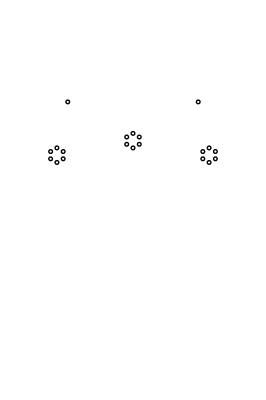

```mathematica
xc={-10.5,-9.63397459621556,-9.63397459621556,-10.5,-11.36602540378444,-11.36602540378444,0.,0.8660254037844386,0.8660254037844386,0.,-0.8660254037844386,-0.8660254037844386,10.5,11.36602540378444,11.36602540378444,10.5,9.63397459621556,9.63397459621556,-9.,9.};
 yc={27.669999999999998,28.169999999999998,29.169999999999998,29.669999999999998,29.169999999999998,28.169999999999998,29.67,30.17,31.17,31.67,31.17,30.17,27.669999999999998,28.169999999999998,29.169999999999998,29.669999999999998,29.169999999999998,28.169999999999998,36.00333333333333,36.00333333333333};
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.25]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-15,15},{0,45}},FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
ncond=Length[xc];
nfeixe=6;
nfases=3;
npr=2;
```

```mathematica
(* rf=.908 *10^-2; *)
rf=29.591*10^-3/2;
rint=7.3914*10^-3/2; 
rpr=4.57*10^-3;
```

```mathematica
ϵ=8.854 10^-12;
```

```mathematica
ρ00=0.06114292531162*10^-3 * π* rf^2;
ρpr=4.19*10^-3* π  *rpr^2;
```

```mathematica
ρsolo= 100;
tempfase=60;
fencalum=0.750223;
αtemp=0.00454562;
σc=fencalum/(ρ00(1+αtemp tempfase));
ρc=1/σc;
```

Dados de simulação

Freqüências de interesse

```mathematica
d1=0.1;
d2=N[4,40];
n=100;
freqlog[i_,f_,np_]:=Table[N[10^(i+x(f-i)/(Floor[np]-1))],{x,-2,np-1}]
freqlin[i_,f_,np_]:=Table[N[(i+x(f-i)/(Floor[np]-1))],{x,1,np-2}]
(*f0=freqlog[d0,d1,500];*)
f1=freqlog[d1,d2,n];
f2=freqlin[10^d1, 10^d2,n];
f=Sort@Join[f1,f2];
```

```mathematica
f;
```

```mathematica
sk=2*π*f;
nf=Length[sk]
```

200

```mathematica
sigma=1/ρsolo;
(*kprima[sigma_,Omega_]:=(sigma)+(10^-6)*(0.057849+I*0.12097)*(Omega^0.71603);*)
kprima[sigma_,Omega_]:=(sigma);
G1=DiagonalMatrix[Table[10^-12,{nfases}]];
```

## Procesamiento de Ynodal

```mathematica
(*YNodal=Table[0,{nf}];
YNodalA=YNodalB=YNodalC=YNodalD=YNodalE=YNodalF=ytraco=YNodal;*)
```

```mathematica
compr2=100000.0;
n=10;
Nelem=2^n;
compr=compr2/Nelem
```

97.6563

```mathematica
(*Exemplo para o primeiro elemento na frequencia*) 
nm=1;
ω=sk[[nm]];
```

```mathematica
(*Calculo da Matriz Nodal para compr*)
MontaMatrizes[ncond,npr,nfeixe,kprima[sigma,ω],ρc,ρpr,rf,rint,rpr,xc,yc,ω];
Yncompr=Ynodal[Z1,Y1,compr];
MatrixForm[Yncompr]
```

(11.4067-4.33902 ⅈ | -3.42462-1.20578 ⅈ | -3.11619-0.716758 ⅈ | -11.4067+4.33902 ⅈ | 3.42462+1.20578 ⅈ | 3.11619+0.716758 ⅈ
-3.42462-1.20578 ⅈ | 11.3783-4.01684 ⅈ | -3.42462-1.20578 ⅈ | 3.42462+1.20578 ⅈ | -11.3783+4.01684 ⅈ | 3.42462+1.20578 ⅈ
-3.11619-0.716758 ⅈ | -3.42462-1.20578 ⅈ | 11.4067-4.33902 ⅈ | 3.11619+0.716758 ⅈ | 3.42462+1.20578 ⅈ | -11.4067+4.33902 ⅈ
-11.4067+4.33902 ⅈ | 3.42462+1.20578 ⅈ | 3.11619+0.716758 ⅈ | 11.4067-4.33902 ⅈ | -3.42462-1.20578 ⅈ | -3.11619-0.716758 ⅈ
3.42462+1.20578 ⅈ | -11.3783+4.01684 ⅈ | 3.42462+1.20578 ⅈ | -3.42462-1.20578 ⅈ | 11.3783-4.01684 ⅈ | -3.42462-1.20578 ⅈ
3.11619+0.716758 ⅈ | 3.42462+1.20578 ⅈ | -11.4067+4.33902 ⅈ | -3.11619-0.716758 ⅈ | -3.42462-1.20578 ⅈ | 11.4067-4.33902 ⅈ)

```mathematica
(*Calculo de elementos de W"LT*)
E2prima=Inverse[IdentityMatrix[3]-((compr^2)/4)*(Z1.Y1)];
F2prima=Inverse[IdentityMatrix[3]-((compr^2)/4)*(Y1.Z1)];
A2prima=IdentityMatrix[3]+((compr^2)/4)*(E2prima.Z1.Y1);
B2prima=-compr*E2prima.Z1;
C2prima=-compr*E2prima.Y1;
D2prima=IdentityMatrix[3]+((compr^2)/4)*(F2prima.Y1.Z1);
```

```mathematica
(*Calculo de W"LT*)
W2prima=ArrayFlatten[{{A2prima,B2prima},{C2prima,D2prima}}];
```

```mathematica
(*Comprobacao de: W2prima compr (Quadripolo compr-> Ynodal compr) = Ynodal compr*) 
YncomprB=Quad2Ym[W2prima];
MatrixForm[-YncomprB](*ATENCAO: Signo trocado para transformar a expresao de Joao a quadripolo regular com a rotina Quad2Ym, nao deberia de se requerir mudar o signo*)
```

(11.4067-4.33902 ⅈ | -3.42462-1.20578 ⅈ | -3.11619-0.716758 ⅈ | -11.4067+4.33902 ⅈ | 3.42462+1.20578 ⅈ | 3.11619+0.716758 ⅈ
-3.42462-1.20578 ⅈ | 11.3783-4.01684 ⅈ | -3.42462-1.20578 ⅈ | 3.42462+1.20578 ⅈ | -11.3783+4.01684 ⅈ | 3.42462+1.20578 ⅈ
-3.11619-0.716758 ⅈ | -3.42462-1.20578 ⅈ | 11.4067-4.33902 ⅈ | 3.11619+0.716758 ⅈ | 3.42462+1.20578 ⅈ | -11.4067+4.33902 ⅈ
-11.4067+4.33902 ⅈ | 3.42462+1.20578 ⅈ | 3.11619+0.716758 ⅈ | 11.4067-4.33902 ⅈ | -3.42462-1.20578 ⅈ | -3.11619-0.716758 ⅈ
3.42462+1.20578 ⅈ | -11.3783+4.01684 ⅈ | 3.42462+1.20578 ⅈ | -3.42462-1.20578 ⅈ | 11.3783-4.01684 ⅈ | -3.42462-1.20578 ⅈ
3.11619+0.716758 ⅈ | 3.42462+1.20578 ⅈ | -11.4067+4.33902 ⅈ | -3.11619-0.716758 ⅈ | -3.42462-1.20578 ⅈ | 11.4067-4.33902 ⅈ)

```mathematica
Wprima=Nest[MatrixPower[#,2]&,W2prima,10];
MatrixForm[Wprima]
MatrixForm[-Quad2Ym[Wprima]](*ATENCAO: Signo trocado para transformar a expresao de Joao a quadripolo regular com a rotina Quad2Ym, nao deberia de se requerir mudar o signo*)
```

(0.999826+0.000359161 ⅈ | -0.000068245-0.0000856555 ⅈ | -0.0000812894-0.0000142439 ⅈ | -70.1914-44.1158 ⅈ | -3.81906-30.7587 ⅈ | -3.81565-27.5518 ⅈ
-0.0000841673-0.0000831125 ⅈ | 0.999842+0.000381144 ⅈ | -0.0000841673-0.0000831125 ⅈ | -3.81906-30.7587 ⅈ | -70.1962-44.1173 ⅈ | -3.81906-30.7587 ⅈ
-0.0000812894-0.0000142439 ⅈ | -0.000068245-0.0000856555 ⅈ | 0.999826+0.000359161 ⅈ | -3.81565-27.5518 ⅈ | -3.81906-30.7587 ⅈ | -70.1914-44.1158 ⅈ
1.33263×10^-9-0.0000104395 ⅈ | -6.41682×10^-10+2.89294×10^-6 ⅈ | -6.70897×10^-11+8.1653×10^-7 ⅈ | 0.999826+0.000359161 ⅈ | -0.0000841673-0.0000831125 ⅈ | -0.0000812894-0.0000142439 ⅈ
-6.41682×10^-10+2.89294×10^-6 ⅈ | 1.58394×10^-9-0.0000111786 ⅈ | -6.41682×10^-10+2.89294×10^-6 ⅈ | -0.000068245-0.0000856555 ⅈ | 0.999842+0.000381144 ⅈ | -0.000068245-0.0000856555 ⅈ
-6.70897×10^-11+8.1653×10^-7 ⅈ | -6.41682×10^-10+2.89294×10^-6 ⅈ | 1.33263×10^-9-0.0000104395 ⅈ | -0.0000812894-0.0000142439 ⅈ | -0.0000841673-0.0000831125 ⅈ | 0.999826+0.000359161 ⅈ)

(0.0111394-0.00423384 ⅈ | -0.00334436-0.00117849 ⅈ | -0.00304315-0.000700231 ⅈ | -0.0111394+0.00423906 ⅈ | 0.00334436+0.00117704 ⅈ | 0.00304315+0.000699822 ⅈ
-0.00334436-0.00117849 ⅈ | 0.0111116-0.00391897 ⅈ | -0.00334436-0.00117849 ⅈ | 0.00334436+0.00117704 ⅈ | -0.0111116+0.00392456 ⅈ | 0.00334436+0.00117704 ⅈ
-0.00304315-0.000700231 ⅈ | -0.00334436-0.00117849 ⅈ | 0.0111394-0.00423384 ⅈ | 0.00304315+0.000699822 ⅈ | 0.00334436+0.00117704 ⅈ | -0.0111394+0.00423906 ⅈ
-0.0111394+0.00423906 ⅈ | 0.00334436+0.00117704 ⅈ | 0.00304315+0.000699823 ⅈ | 0.0111394-0.00423384 ⅈ | -0.00334436-0.00117849 ⅈ | -0.00304315-0.000700231 ⅈ
0.00334436+0.00117704 ⅈ | -0.0111116+0.00392456 ⅈ | 0.00334436+0.00117704 ⅈ | -0.00334436-0.00117849 ⅈ | 0.0111116-0.00391897 ⅈ | -0.00334436-0.00117849 ⅈ
0.00304315+0.000699823 ⅈ | 0.00334436+0.00117704 ⅈ | -0.0111394+0.00423906 ⅈ | -0.00304315-0.000700231 ⅈ | -0.00334436-0.00117849 ⅈ | 0.0111394-0.00423384 ⅈ)

```mathematica
(*Obtem a Ynodal do compr2 para comparar resultados*)
MontaMatrizes[ncond,npr,nfeixe,kprima[sigma,ω],ρc,ρpr,rf,rint,rpr,xc,yc,ω];
Yncompr2=Ynodal[Z1,Y1,compr2];
Yncompr2B=Y2Quad[Yncompr2];   (*Quadripolo final que deberia ser obtido*)
```

```mathematica
MatrixForm[Yncompr2B]
MatrixForm[Yncompr2]
```

(0.999825+0.000359336 ⅈ | -0.0000682783-0.0000856973 ⅈ | -0.0000813291-0.0000142508 ⅈ | 70.1914+44.1158 ⅈ | 3.81906+30.7587 ⅈ | 3.81564+27.5518 ⅈ
-0.0000842083-0.0000831532 ⅈ | 0.999842+0.00038133 ⅈ | -0.0000842083-0.0000831532 ⅈ | 3.81906+30.7587 ⅈ | 70.1962+44.1173 ⅈ | 3.81906+30.7587 ⅈ
-0.0000813291-0.0000142508 ⅈ | -0.0000682783-0.0000856973 ⅈ | 0.999825+0.000359336 ⅈ | 3.81564+27.5518 ⅈ | 3.81906+30.7587 ⅈ | 70.1914+44.1158 ⅈ
-1.33458×10^-9+0.0000104395 ⅈ | 6.42623×10^-10-2.89294×10^-6 ⅈ | 6.71881×10^-11-8.1653×10^-7 ⅈ | 0.999825+0.000359336 ⅈ | -0.0000682783-0.0000856973 ⅈ | -0.0000813291-0.0000142508 ⅈ
6.42623×10^-10-2.89294×10^-6 ⅈ | -1.58626×10^-9+0.0000111786 ⅈ | 6.42623×10^-10-2.89294×10^-6 ⅈ | -0.0000842083-0.0000831532 ⅈ | 0.999842+0.00038133 ⅈ | -0.0000842083-0.0000831532 ⅈ
6.71881×10^-11-8.1653×10^-7 ⅈ | 6.42623×10^-10-2.89294×10^-6 ⅈ | -1.33458×10^-9+0.0000104395 ⅈ | -0.0000813291-0.0000142508 ⅈ | -0.0000682783-0.0000856973 ⅈ | 0.999825+0.000359336 ⅈ)

(0.0111394-0.00423384 ⅈ | -0.00334436-0.00117849 ⅈ | -0.00304315-0.000700231 ⅈ | -0.0111394+0.00423906 ⅈ | 0.00334436+0.00117704 ⅈ | 0.00304315+0.000699823 ⅈ
-0.00334436-0.00117849 ⅈ | 0.0111116-0.00391897 ⅈ | -0.00334436-0.00117849 ⅈ | 0.00334436+0.00117704 ⅈ | -0.0111116+0.00392456 ⅈ | 0.00334436+0.00117704 ⅈ
-0.00304315-0.000700231 ⅈ | -0.00334436-0.00117849 ⅈ | 0.0111394-0.00423384 ⅈ | 0.00304315+0.000699823 ⅈ | 0.00334436+0.00117704 ⅈ | -0.0111394+0.00423906 ⅈ
-0.0111394+0.00423906 ⅈ | 0.00334436+0.00117704 ⅈ | 0.00304315+0.000699823 ⅈ | 0.0111394-0.00423384 ⅈ | -0.00334436-0.00117849 ⅈ | -0.00304315-0.000700231 ⅈ
0.00334436+0.00117704 ⅈ | -0.0111116+0.00392456 ⅈ | 0.00334436+0.00117704 ⅈ | -0.00334436-0.00117849 ⅈ | 0.0111116-0.00391897 ⅈ | -0.00334436-0.00117849 ⅈ
0.00304315+0.000699823 ⅈ | 0.00334436+0.00117704 ⅈ | -0.0111394+0.00423906 ⅈ | -0.00304315-0.000700231 ⅈ | -0.00334436-0.00117849 ⅈ | 0.0111394-0.00423384 ⅈ)